## Installation

Install packages needed, first adding the BH Perturbation Toolkit paclet server.

```mathematica
If[$VersionNumber≥12.1,
PacletSiteRegister["https://pacletserver.bhptoolkit.org","Black Hole Perturbation Toolkit Paclet Server"],
PacletSiteAdd["http://pacletserver.bhptoolkit.org","Black Hole Perturbation Toolkit Paclet Server"]
]
```

PacletSiteObject[<|URL→https://pacletserver.bhptoolkit.org,Name→Black Hole Perturbation Toolkit Paclet Server,Local→False,Type→Server|>]

For updating the available packages:

```mathematica
If[$VersionNumber≥12.1,
PacletSiteUpdate["https://pacletserver.bhptoolkit.org"],
PacletSiteUpdate["http://pacletserver.bhptoolkit.org"]
]
```

PacletSiteObject[<|URL→https://pacletserver.bhptoolkit.org,Name→Black Hole Perturbation Toolkit Paclet Server,Local→False,Type→Server|>]

Now install all the required packages:

```mathematica
PacletInstall["GeneralRelativityTensors"];
PacletInstall["KerrGeodesics"];
PacletInstall["SpinWeightedSpheroidalHarmonics"];
PacletInstall["ReggeWheeler"];
PacletInstall["Teukolsky"];
PacletInstall["PostNewtonianSelfForce"];
```

## Initial system information

We define the two BH masses below, which we are free to choose such that the total mass M=1 for simplicity. Here we look at a (large) mass ratio of 24. From these we define the total mass M, the (small) mass ratio ϵ, the large mass ratio q, and the symmetric mass ratio, ν:

```mathematica
m11=0.96;
m12=0.04;
m21=0.9996;
m22=0.0004;

M = 1;
ν1 = (m12 m11)/(m11 + m12)^2;
ν2 = (m22 m21)/(m21 + m22)^2;
```

We also set initial parameters for the orbital parameters, which we will need in order to solve our ODEs.

```mathematica
Ωinit=0.015;
ϕinit=0.004;
```

Use the Teukolsky package when computing our interpolating flux lists by finding solutions to the Teukolsky equation.

```mathematica
<<Teukolsky`
<<KerrGeodesics`
```

Consider the (l,m) = (2,2) mode (the dominant mode). Set the parameters;

```mathematica
s = -2;
l = 2;
m = 2;
e=0;   (* Zero eccentricity *)
θinc=0; (* Equatorial orbit *) (*set to pi for negative a, ie. retrograde orbit*)
n=0;k=0; (* Circular orbits don't have frequencies related to radial or polar motion *)
```

## Comparing Schwarzschild and (prograde) Kerr waveforms

### Solving the ODEs

Note we denote any parameters or functions etc. with the letter S or K, corresponding to the Schwarzschild or Kerr cases respectively. Set our values for the BH spin and initial separation.

```mathematica
Sa = 0;   (* schwarzschild spacetime *)
Ka=0.5`64;   (* kerr spacetime *)
Sr0init = M^(1/3)(1/Ωinit - Sa)^(2/3)
Kr0init = M^(1/3)(1/Ωinit - Ka)^(2/3)
```

16.4414

16.3591

In order to reduce calculations, we interpolate a list of flux values, consisting of the sum of the infinity and horizon fluxes, summed over a wide range of l and m modes (note that the mode sum is a converging one, so we stop after l = 10). This is done for values of the radius from 4.2 to 30 for the Kerr case, and 6 to 30 for the Schwarzschild case, in increments of 10^-1. This code was run in a separate notebook but can easily be reproduced.

```mathematica
Sℱ=Interpolation[ ,InterpolationOrder->8];
Kℱ=Interpolation[,InterpolationOrder->8];
ShAmp=Interpolation[,InterpolationOrder->8];
KhAmp=Interpolation[,InterpolationOrder->8];
```

```mathematica
{SΩsol1,Sϕsol1,Sr0sol1}=NDSolveValue[{
SΩ01'[t]==(3 (-3 M+Sr01[t])^(3/2) ν1 Sℱ[Sr01[t]])/(M^(1/2)Sr01[t] (-6 M+Sr01[t])),
Sϕ01'[t]==SΩ01[t],
SΩ01[t]==Sqrt[M/Sr01[t]^3],
Sr01[0]==Sr0init,
Sϕ01[0]==ϕinit,
WhenEvent[Sr01[t]≤6.01M, "StopIntegration"]},{SΩ01,Sϕ01,Sr01},{t,0,∞},PrecisionGoal->10,AccuracyGoal->10];
{tmin,Stmax1}=Sr0sol1["Domain"][[1]];
{KΩsol1,Kϕsol1,Kr0sol1}=NDSolveValue[{
KΩ01'[t]==(3 Kr01[t]^3 (-3 M+2 Ka √(M/Kr01[t])+Kr01[t])^(3/2)ν1 Kℱ[Kr01[t]])/(√M (Ka √M+Kr01[t]^(3/2))^2 (-3 Ka^2+8 Ka √(M Kr01[t])+Kr01[t] (-6 M+Kr01[t]))),
Kϕ01'[t]==KΩ01[t],
KΩ01[t]== (Ka+(Kr01[t]/M^(1/3))^(3/2))^-1,
Kr01[0]==Kr0init,
Kϕ01[0]==ϕinit,
WhenEvent[Kr01[t]≤ 4.234, "StopIntegration"]},{KΩ01,Kϕ01,Kr01},{t,0,∞},PrecisionGoal->10,AccuracyGoal->10];
{tmin,Ktmax1}=Kr0sol1["Domain"][[1]];
{SΩsol2,Sϕsol2,Sr0sol2}=NDSolveValue[{
SΩ02'[t]==(3 (-3 M+Sr02[t])^(3/2) ν2 Sℱ[Sr02[t]])/(M^(1/2)Sr02[t] (-6 M+Sr02[t])),
Sϕ02'[t]==SΩ02[t],
SΩ02[t]==Sqrt[M/Sr02[t]^3],
Sr02[0]==Sr0init,
Sϕ02[0]==ϕinit,
WhenEvent[Sr02[t]≤6.01M, "StopIntegration"]},{SΩ02,Sϕ02,Sr02},{t,0,∞},PrecisionGoal->10,AccuracyGoal->10];
{tmin,Stmax2}=Sr0sol2["Domain"][[1]];
{KΩsol2,Kϕsol2,Kr0sol2}=NDSolveValue[{
KΩ02'[t]==(3 Kr02[t]^3 (-3 M+2 Ka √(M/Kr02[t])+Kr02[t])^(3/2)ν2 Kℱ[Kr02[t]])/(√M (Ka √M+Kr02[t]^(3/2))^2 (-3 Ka^2+8 Ka √(M Kr02[t])+Kr02[t] (-6 M+Kr02[t]))),
Kϕ02'[t]==KΩ02[t],
KΩ02[t]== (Ka+(Kr02[t]/M^(1/3))^(3/2))^-1,
Kr02[0]==Kr0init,
Kϕ02[0]==ϕinit,
WhenEvent[Kr02[t]≤ 4.234, "StopIntegration"]},{KΩ02,Kϕ02,Kr02},{t,0,∞},PrecisionGoal->10,AccuracyGoal->10];
{tmin,Ktmax2}=Kr0sol2["Domain"][[1]];
Stmax1
Ktmax1
Stmax2
Ktmax2
```

30100.6

36000.7

2.89081×10^6

3.45745×10^6

Now we plot the solutions of these equations to see how they evolve in time.

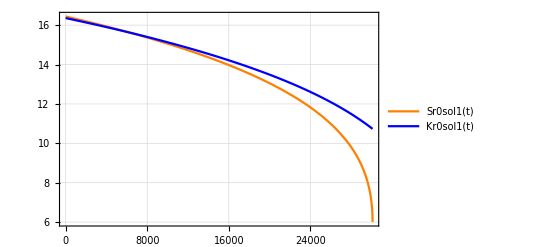

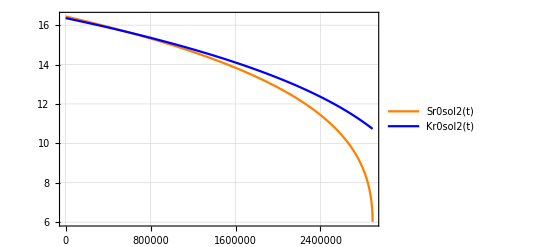

```mathematica
Plot[{Sr0sol1[t],Kr0sol1[t]},{t,tmin,Stmax1},PlotTheme->"Detailed",ImageSize->400,PlotStyle->{Orange,Blue}]
Plot[{Sr0sol2[t],Kr0sol2[t]},{t,tmin,Stmax2},PlotTheme->"Detailed",ImageSize->400,PlotStyle->{Orange,Blue}]
```

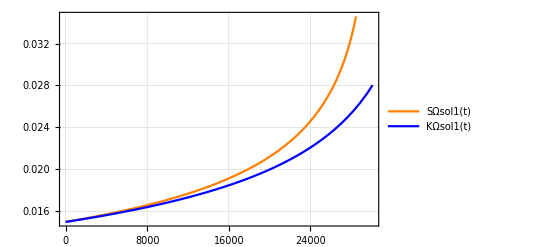

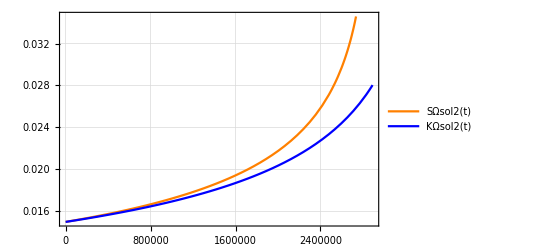

```mathematica
Plot[{SΩsol1[t],KΩsol1[t]},{t,tmin,Stmax1},PlotTheme->"Detailed",ImageSize->400,PlotStyle->{Orange,Blue}]
Plot[{SΩsol2[t],KΩsol2[t]},{t,tmin,Stmax2},PlotTheme->"Detailed",ImageSize->400,PlotStyle->{Orange,Blue}]
```

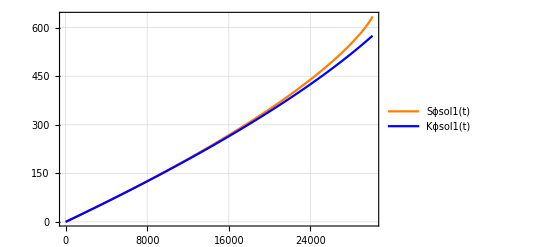

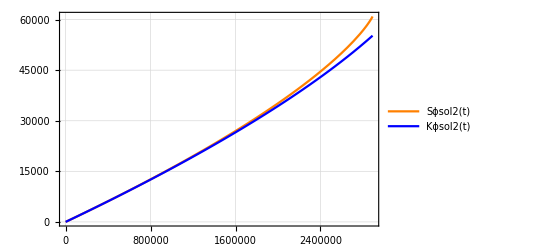

```mathematica
Plot[{Sϕsol1[t],Kϕsol1[t]},{t,tmin,Stmax1},PlotTheme->"Detailed",ImageSize->400, PlotStyle->{Orange,Blue}]
Plot[{Sϕsol2[t],Kϕsol2[t]},{t,tmin,Stmax2},PlotTheme->"Detailed",ImageSize->400, PlotStyle->{Orange,Blue}]
```

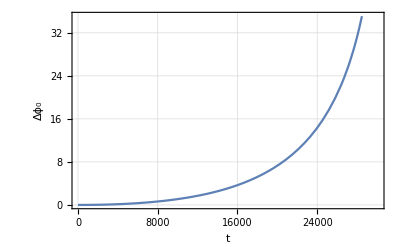

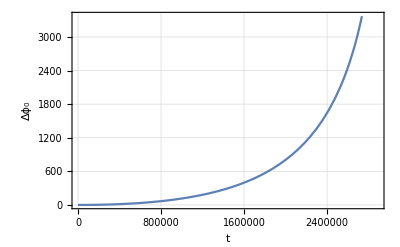

```mathematica
Plot[{Sϕsol1[t]-Kϕsol1[t]},{t,tmin,Stmax1},PlotTheme->"Detailed",ImageSize->400, PlotLegends->"Schw and Kerr Phase difference",FrameLabel->{"t","Δϕ_0"}]
Plot[{Sϕsol2[t]-Kϕsol2[t]},{t,tmin,Stmax2},PlotTheme->"Detailed",ImageSize->400, PlotLegends->"Schw and Kerr Phase difference",FrameLabel->{"t","Δϕ_0"}]
```

Now add parametric plots of the inspiral in the equatorial plane, note in our units the schwarzschild BH radius is 2M = 2, and we let the radius for the kerr case be M+(M^2-a^2)^(1/2).

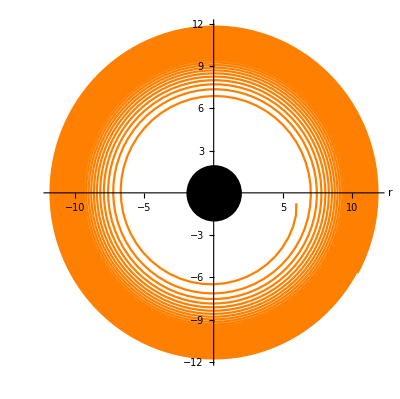

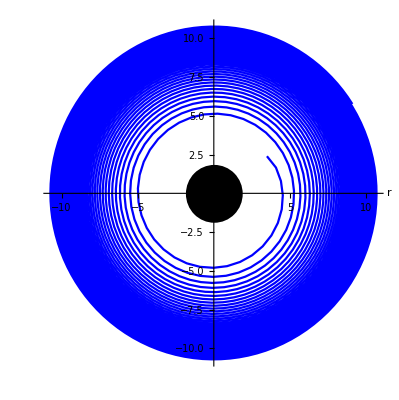

-Graphics-

-Graphics-

```mathematica
Show[ParametricPlot[{Sr0sol1[t]Cos[Sϕsol1[t]],Sr0sol1[t]Sin[Sϕsol1[t]]},{t,24000,Stmax1}, PlotStyle->Orange, AxesLabel->{"r"}],Graphics[Disk[{0,0},2]]]
Show[ParametricPlot[{Kr0sol1[t]Cos[Kϕsol1[t]],Kr0sol1[t]Sin[Kϕsol1[t]]},{t,30000,Ktmax1}, PlotStyle->Blue,AxesLabel->{"r"}],Graphics[Disk[{0,0},M+(M^2-Ka^2)^(1/2)]]]
Show[ParametricPlot[{Sr0sol2[t]Cos[Sϕsol2[t]],Sr0sol2[t]Sin[Sϕsol2[t]]},{t,2700000,Stmax2},PlotPoints->4000, PlotStyle->Orange, AxesLabel->{"r"}],Graphics[Disk[{0,0},2]]]
Show[ParametricPlot[{Kr0sol2[t]Cos[Kϕsol2[t]],Kr0sol2[t]Sin[Kϕsol2[t]]},{t,3300000,Ktmax2},PlotPoints->4000, PlotStyle->Blue,AxesLabel->{"r"}],Graphics[Disk[{0,0},M+(M^2-Ka^2)^(1/2)]]]
```

### Construct and plot the waveform

We construct our waveform by first multiplying the amplitude by the phase

```mathematica
Sh1[t_]:=ν1 ShAmp[Sr0sol1[t]] ⅇ^(-ⅈ (m Sϕsol1[t]+Arg[ShAmp[Sr0sol1[0]]]));
Kh1[t_]:=ν1 KhAmp[Kr0sol1[t]] ⅇ^(-ⅈ (m Kϕsol1[t]+Arg[KhAmp[Kr0sol1[0]]]));
Sh2[t_]:=ν2 ShAmp[Sr0sol2[t]] ⅇ^(-ⅈ (m Sϕsol2[t]+Arg[ShAmp[Sr0sol2[0]]]));
Kh2[t_]:=ν2 KhAmp[Kr0sol2[t]] ⅇ^(-ⅈ (m Kϕsol2[t]+Arg[KhAmp[Kr0sol2[0]]]));
```

Plot our kerr and schwarzschild waveforms

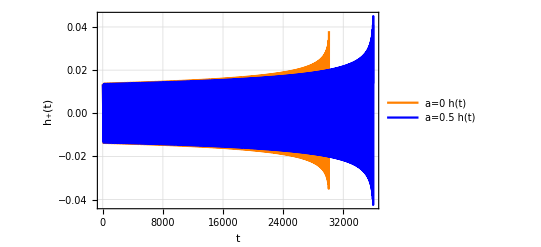

-Graphics-

```mathematica
Plot[{Piecewise[{{Re[Sh1[t]],t<Stmax1}},Indeterminate],Re[Kh1[t]]},{t,tmin,Ktmax1},PlotPoints->4000,PlotTheme->"Detailed",ImageSize->400, PlotRange->All, PlotLegends->{"a=0 h(t)","a=0.5 h(t)"}, PlotStyle->{Orange,Blue},AxesLabel->{"t","h_+(t)"},FrameLabel->{"t","h_+(t)"}]
Plot[{Piecewise[{{Re[Sh2[t]],t<Stmax2}},Indeterminate],Re[Kh2[t]]},{t,22000,Ktmax2},PlotPoints->2000,PlotTheme->"Detailed",ImageSize->400, PlotRange->All, PlotLegends->{"a=0 h(t)","a=0.5 h(t)"}, PlotStyle->{Orange,Blue},AxesLabel->{"t","h_+(t)"},FrameLabel->{"t","h_+(t)"}]
```